```mathematica
ClearAll["Global`*"]
SetDirectory[NotebookDirectory[]];SetOptions[$FrontEndSession,NotebookAutoSave->True];
NotebookSave[];
AppendTo[$Path,FileNameJoin[{$HomeDirectory,"Dropbox","EpidCRNmodels"}]];Needs["EpidCRN`"];(*Get["HopfE`"];*)
(*Latex dictionary*)
Format[mu]:=μ;Format[xi]:=ξ;Format[de]:=δ;Format[eta]:=η;
Format[ga]:=ga;Format[k1]:=Subscript[k,d];Format[k2]:=Subscript[k,g];
Format[muS]:=Subscript[μ,s];Format[laS]:=Subscript[θ,2];Format[th12]:=Subscript[θ,12];
Format[th21]:=Subscript[θ,21];
Format[th]:=θ;Format[mu1]:=Subscript[μ,1];Format[mu2]:=Subscript[μ,2];
Format[m1]:=Subscript[m,1];Format[m2]:=Subscript[m,2];
Format[mu12]:=Subscript[μ,12];
Format[La]:=Λ;Format[be1]:=Subscript[β,1];(*Format[be2]:=Subscript[β,2];*)
Format[be2]:=Subscript[β,2];Format[be12]:=Subscript[β,12];

(* Example A: shared buffer "X" (RN and rts required names) *)
RN = {
  "A" + "X" -> 2*"A",
  "X" -> "A",
  "B" + "X" -> 2*"B",
  "X" -> "B",
  "A" -> "B",
  0 -> "X",   (* inflow to X to avoid singularity in F/V/K *)
  "X" -> 0    (* outflow/removal of X *)
};
rts = {
  k1*a*x,    (* A + X -> 2 A *)
  k2*x,      (* X -> A *)
  k3*b*x,    (* B + X -> 2 B *)
  k4*x,      (* X -> B *)
  k5*a,      (* A -> B (one-way cross: induces T1 -> T2) *)
  k6,        (* inflow: 0 -> X *)
  k7*x       (* outflow: X -> 0 *)
};

Print["reactions and transitions: ",Transpose[{RN,rts}]//MatrixForm]
(*Get bdAn outputs*)

{RHS, var, par, cp, mSi, Jx, Jy, E0, K, R0A, infVars,gam,ng}= bdAn[RN,rts];
Print["siphons are",mSi,"E0 is",E0," R1,R2, ... are",R0A/.E0];
Print["K=",K//MatrixForm,"F=",ng[[2]]//MatrixForm,"V=",ng[[3]]//MatrixForm];
IGMS[RN, mSi];
```

reactions and transitions: (A+X→2 A | a k_d x
X→A | k_g x
B+X→2 B | b k3 x
X→B | k4 x
A→B | a k5
0→X | k6
X→0 | k7 x)

siphons are{}E0 is{} R1,R2, ... areEigenvalues[0.Inverse[-{}{}]]

K=0.Inverse[-{}{}]F=0V=-{}{}

Minimal siphons: {}

IGMS edges: {}

IGMS is acyclic (no cycles found)

-Graphics-

reactions and transitions: (S+Y→2 S | r1 s y
Y→S | r2 y
T+Y→2 T | r3 t y
T→U | r4 t
U→0 | r5 u)

Singular case

siphons are{{Y},{T}}E0 is{T→0,Y→0} R1,R2, ... areEigenvalues[singular]

K=singularF=(0 | 0
0 | 0)V=(0 | 0
0 | 0)

Minimal siphons: {T_1={Y},T_2={T}}

IGMS edges: {1→2}

IGMS is acyclic (no cycles found)

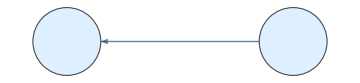

```mathematica
(* Example 2: intersection with asymmetric cross-production *)
RN = {
  "S" + "Y" -> 2*"S",
  "Y" -> "S",
  "T" + "Y" -> 2*"T",
  "T" -> "U",
  "U" -> 0
};
rts = {
  r1*s*y,    (* autocatalysis S + Y -> 2 S *)
  r2*y,      (* Y -> S *)
  r3*t*y,    (* autocatalysis T + Y -> 2 T *)
  r4*t,      (* T -> U (forward cross) *)
  r5*u       (* U -> 0 (removal) *)
};

Print["reactions and transitions: ",Transpose[{RN,rts}]//MatrixForm]
(*Get bdAn outputs*)

{RHS, var, par, cp, mSi, Jx, Jy, E0, K, R0A, infVars,gam,ng}= bdAn[RN,rts];
Print["siphons are",mSi,"E0 is",E0," R1,R2, ... are",R0A/.E0];
jac=Grad[RHS,var];Print["K=",K//MatrixForm,"F=",ng[[2]]//MatrixForm,"V=",ng[[3]]//MatrixForm];
IGMS[RN, mSi];
```